```mathematica
Ωm=0.3;
Clear[a]
ΩΛ=0.7;
Ωk=0;
H0=70;
DSolve[{a'[t]==H0 √(Ωm /a[t] +ΩΛ a[t]^2),a[0]==1},a[t],t]

alcdm[t_]:=0.7539474411291538 Sinh[1.5 (0.806623414223964+58.56620185738529 t)]^(2/3)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{a[t]→(-0.376974-0.652938 ⅈ) Sinh[1.5 (-0.806623+58.5662 t)]^(2/3)},{a[t]→0.753947 Sinh[1.5 (0.806623+58.5662 t)]^(2/3)}}

```mathematica
Solve[alcdm[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-0.0137728}}

```mathematica
s=NDSolve[{a'[t]==H0 √(Ωm /a[t]+ΩΛ a[t]^1.1),a[0]==1},a,{t,-0.02,0.01}]
```

{{a→InterpolatingFunction[…]}}

```mathematica
k=NDSolve[{a'[t]==H0 √(Ωm /a[t] +ΩΛ a[t]^2.6),a[0]==1},a,{t,-0.02,0.01}]
```

{{a→InterpolatingFunction[…]}}

```mathematica
Ωm=0.8;
Clear[a]
ΩΛ=0.2;
Ωk=0;
```

```mathematica
DSolve[{a'[t]==H0 √(Ωm /a[t]+Ωk +ΩΛ a[t]^2),a[0]==1},a[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{a[t]→(-0.376974-0.652938 ⅈ) Sinh[1.5 (-0.806623+58.5662 t)]^(2/3)},{a[t]→0.753947 Sinh[1.5 (0.806623+58.5662 t)]^(2/3)}}

```mathematica
alcdm1[t_]:=1.5874010519681994 Sinh[1.5 (0.320807883373069+31.304951684997057 t)]^(2/3)
```

```mathematica
Ωm=0.3;
Clear[a]
ΩΛ=0.7;
Ωk=163.22;
H0=70;
l=NDSolve[{a'[t]==H0 √(Ωm /a[t]+Ωk /a[t]^2+ΩΛ a[t]^2),a[0]==1},a[t],{t,-0.01,0.01}]
```

NDSolve::ndsz: At t == -0.000558354, step size is effectively zero; singularity or stiff system suspected.

{{a[t]→InterpolatingFunction[…][t]}}

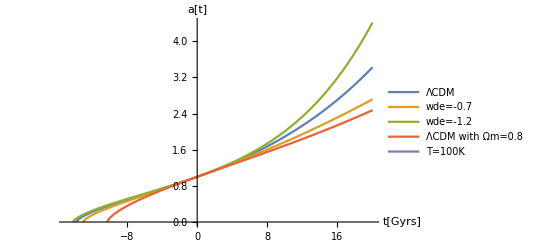

```mathematica
Plot[{alcdm[t/1000],Evaluate[a[t/1000]/.s],Evaluate[a[t/1000]/.k],alcdm1[t/1000],Evaluate[a[t/1000]/.l]},{t,-15,20},AxesLabel->{"t[Gyrs]","a[t]"},PlotLegends->{"ΛCDM","wde=-0.7","wde=-1.2","ΛCDM with Ωm=0.8","T=100K"}]
```

(44.1558 Cosh[1.5 (0.806623+58.5662 t)])/Sinh[1.5 (0.806623+58.5662 t)]^(1/3)

(49.6935 Cosh[1.5 (0.320808+31.305 t)])/Sinh[1.5 (0.320808+31.305 t)]^(1/3)

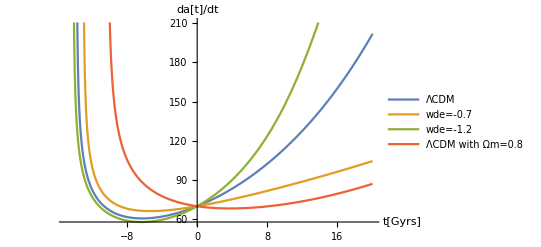

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-0.0102478}}

```mathematica
alcdm'[t]
alcdm1'[t]
Plot[{alcdm'[t/1000],Evaluate[a'[t/1000]/.s],Evaluate[a'[t/1000]/.k],alcdm1'[t/1000]},{t,-15,20},AxesLabel->{"t[Gyrs]","da[t]/dt"},PlotLegends->{"ΛCDM","wde=-0.7","wde=-1.2","ΛCDM with Ωm=0.8"}]


Solve[alcdm1[t]==0,t]
```